## Mirror machine model with axial asymmetry

```mathematica
Clear["Global`*"]
k = (2π)/L;
AAxiAsym[r_,θ_,z_]={ϵ r^2 Cos[θ] Cos[k*z], (1/2.)*B0*r - ((B0*α)/k)*(Cos[k*z]*BesselI[1,k*r]+η Sin[k*z/2]*BesselI[1,k*r/2]),0.};
fieldAxiAsymCyl[r_,θ_,z_]=Expand[Curl[AAxiAsym[r,θ,z],{r,θ,z},"Cylindrical"]];
fieldAxiAsymCyl[r_,θ_,z_]=fieldAxiAsymCyl[r,θ,z]//.{BesselI[1,2 π r/L]/r->((2 π /L)/2)*(BesselI[0,2 π r/L]-BesselI[2,2 π r/L]),BesselI[1,π r/L ]/r->(π /(2L))*(BesselI[0,π r/L]-BesselI[2,π r/L])}//FullSimplify;
fieldMagAACyl[r_,θ_,z_]=Sqrt[Dot[fieldAxiAsymCyl[r,θ,z],fieldAxiAsymCyl[r,θ,z]]];
(*fieldAxiAsymCar[x_,y_,z_] = fieldAxiAsym[r,θ,z]/.{r-> Sqrt[x^2+y^2],θ->ArcTan[x,y],z-> z}*)
fieldAxiAsymCar[x_,y_,z_] = {fieldAxiAsymCyl[r,θ,z][[1]]*Cos[θ]-fieldAxiAsymCyl[r,θ,z][[2]]*Sin[θ],
fieldAxiAsymCyl[r,θ,z][[1]]*Sin[θ]+fieldAxiAsymCyl[r,θ,z][[2]]*Cos[θ],
fieldAxiAsymCyl[r,θ,z][[3]]}//.{r-> Sqrt[x^2+y^2],θ->ArcTan[x,y],z-> z};
fieldMagAACar[x_,y_,z_]=Simplify[fieldMagAACyl[r,θ,z]/.{r-> Sqrt[x^2+y^2],θ->ArcTan[x,y],z-> z}]
Simplify[Expand[Sqrt[Dot[fieldAxiAsymCar[x,y,z],fieldAxiAsymCar[x,y,z]]]]];
fieldMagAACyl[0,0,z]//FullSimplify
B0=1.;
α=0.5;L = π;ϵ=0.0;η=1.5;mutilde = 0.01;
```

√((1. B0+y ϵ Cos[(2 π z)/L]-1. B0 α BesselI[0,(2 π √(x^2+y^2))/L] Cos[(2 π z)/L]-0.5 B0 α η BesselI[0,(π √(x^2+y^2))/L] Sin[(π z)/L])^2+(4 π^2 x^2 (x^2+y^2) ϵ^2 Sin[(2 π z)/L]^2)/L^2+1/4 B0^2 α^2 (η BesselI[1,(π √(x^2+y^2))/L] Cos[(π z)/L]-2 BesselI[1,(2 π √(x^2+y^2))/L] Sin[(2 π z)/L])^2)

√(B0^2 (1.-1. α Cos[(2 π z)/L]-0.5 α η Sin[(π z)/L])^2)

### Solving for the maxima and minimum in the field magnitude

```mathematica
saddleTop=FindMaximum[fieldMagAACyl[r,θ,z],{{r,0},{θ,0},{z,π/k}}]
(*wellMid =FindMinimum[fieldMagCylAA[r,θ,z],{{r,0},{θ,0},{z,0.}}]*)
(*wellMid =FindMinimum[fieldMagCylAA[r,θ,z],{{r,1.},{θ,0},{z,0.}}]*)
saddleBot =FindMaximum[fieldMagAACyl[r,θ,z],{{r,0},{θ,0},{z,-π/k}}]
fieldMinPt = FindMinimum[fieldMagAACyl[r,θ,z],{{r,1.},{θ,π/2.},{z,0.}}]
h0=fieldMagAACyl[r,θ,z]/.saddleTop[[2]]
h1=fieldMagAACyl[r,θ,z]/.saddleBot[[2]]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{1.125,{r→0.,θ→0.,z→1.5708}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{1.875,{r→0.,θ→0.,z→-1.5708}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.33263×10^-15,{r→0.884929,θ→1.5708,z→0.143259}}

1.125

1.875

### Plotting | B | contours, field lines, and | B | on the axis

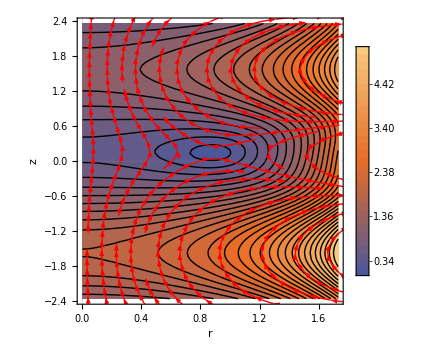

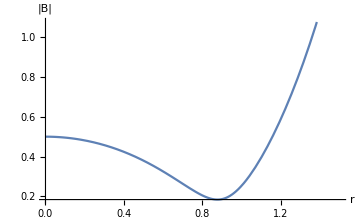
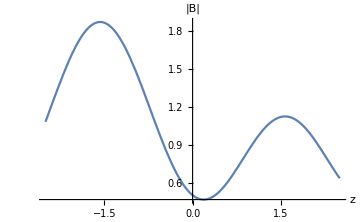

```mathematica
θslice = π/4;
cplot2d =ContourPlot[fieldMagAACyl[r,θslice,z],{r,0,Sqrt[3]},{z,-1.5*(π/k),1.5*(π/k)},Contours->30,PlotPoints->10,MaxRecursion->2,PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->"Scientific",FrameLabel->{Style[r,20],Style[z,20]},ImageSize->Medium];
splot2d =StreamPlot[{fieldAxiAsymCyl[r,θslice,z][[1]],fieldAxiAsymCyl[r,0,z][[3]]},{r,0,2},{z,-2*(L/2),2*(L/2)},StreamColorFunction-> None,StreamStyle->Red,PlotLegends->Automatic,PlotTheme->"Scientific",FrameLabel->{Style[r,20],Style[z,20]},ImageSize->Medium];
Show[cplot2d,splot2d]
{Plot[fieldMagAACyl[r,0,0],{r,0,1.5},AxesLabel->{r,"|B|"},ImageSize->Medium],Plot[fieldMagAACyl[0,0,z],{z,-2.5,2.5},AxesLabel->{z,"|B|"},ImageSize->Medium]}
```

### For schematics

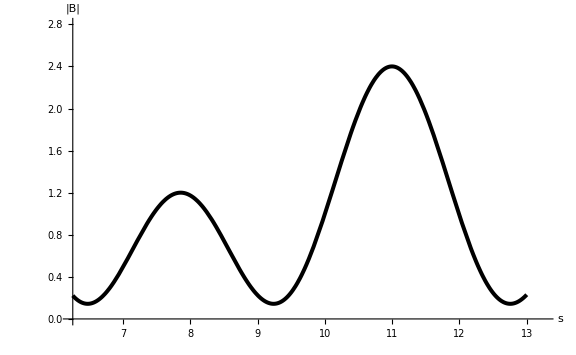

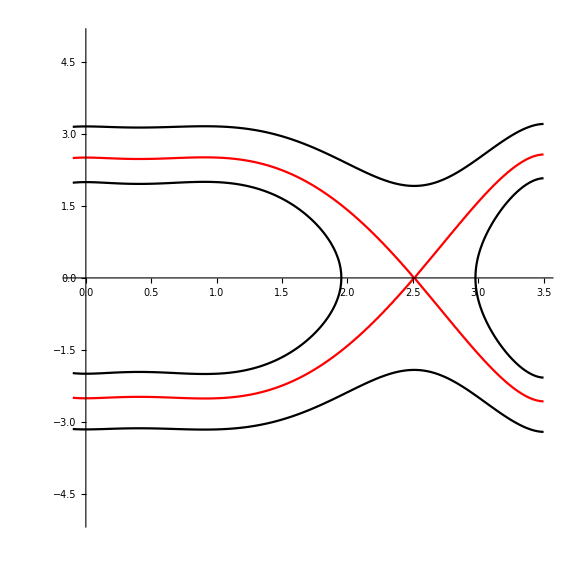

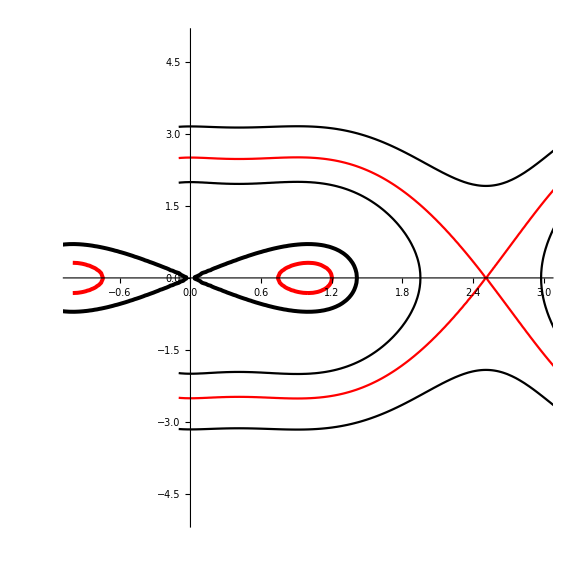

```mathematica
Plot[fieldMagAACyl[0,0,z],{z,6.25,13},AxesLabel->{s,"|B|"},PlotStyle->Directive[Black,Thickness[0.005]],AxesStyle->Directive[Thick,Black,FontSize->25],TicksStyle->Directive[FontOpacity->0,FontSize->0],PlotRange->{{6.25,13.25},{0,2.8}},ImageSize->Large]
A=1.;
B=1.;
cplot1=ContourPlot[{y^2/2-A x^2/2+B x^4/4==-0.2},{x,-1,3},{y,-5,5},PlotPoints->50,ContourStyle->Directive[Red,Thickness[0.005]],Frame->False,Axes->True];
cplot2=ContourPlot[{y^2/2-A x^2/2+B x^4/4==0},{x,-1.2,3},{y,-5,5},PlotPoints->50,ContourStyle->Directive[Black,Thickness[0.005]]];
A=1.4;
B=-1.2;
c=0.2;
v[x_,y_]=y^2/2+c x^2((x-2.2)^2-A^2)((x-2.2)^2-B^2);
cplot3=ContourPlot[{v[x,y]==2.,v[x,y]==3.156,v[x,y]==5},{x,-0.1,3.5},{y,-5,5},PlotPoints->50,ContourStyle->{Black,Red},Frame->False,Axes->True]
(*cplot3=ContourPlot[{v[x,y]},{x,-2,5.5},{y,-5,5},PlotPoints->50,Contours->30,Frame->False,Axes->True]*)
Show[cplot1,cplot2,cplot3]
(*ParametricPlot[{{0.5+ Sqrt[2A]Sech[Sqrt[A]t],Sqrt[2A]Sech[Sqrt[A] t]Tanh[Sqrt[A] t]},{1+ 0.5Sqrt[2A]Sech[Sqrt[A]t],0.5Sqrt[2A]Sech[Sqrt[A] t]Tanh[Sqrt[A] t]},{0.5+ Sqrt[2A]*Sech[Sqrt[A ]t],-Sqrt[2A]*Sech[Sqrt[A] t]Tanh[Sqrt[A] t]},
{0.5- Sqrt[2A]*Sech[Sqrt[A ]t],-Sqrt[2A]*Sech[Sqrt[A] t]Tanh[Sqrt[A] t]}},{t,-10π,6π},PlotRange->{{-0.5,4},{-2,2}},PlotStyle->Directive[Black]]*)
```

### Plotting the critical surfaces in the field, that is d | B | /ds = 0

```mathematica
b[r_,θ_,z_]=fieldAxiAsymCyl[r,θ,z]/fieldMagAACyl[r,θ,z];
fieldMinPt = FindMinimum[fieldMagAACyl[r,θ,z],{{r,1.},{θ,π/2.},{z,0.}}]
gradModB[r_,θ_,z_]=Grad[fieldMagAACyl[r,θ,z],{r,θ,z},"Cylindrical"];
dmodBdsCyl[r_,θ_,z_] = Dot[b[r,θ,z],gradModB[r,θ,z]];
dmodBds[x_,y_,z_]=dmodBdsCyl[r,θ,z]/.{r->Sqrt[x^2 +y^2],θ->ArcTan[x,y],z->z};
graddmodBds[r_,θ_,z_]=Grad[dmodBdsCyl[r,θ,z],{r,θ,z},"Cylindrical"];
d2modBds2Cyl[r_,θ_,z_] = Dot[b[r,θ,z],graddmodBds[r,θ,z]];
d2modBds2[x_,y_,z_]=d2modBds2Cyl[r,θ,z]/.{r->Sqrt[x^2 +y^2],θ->ArcTan[x,y],z->z};
(*ContourPlot[dmodBds[r,0,z],{r,0,1},{z,-1.5 L/2,1.5 L/2},Contours->{0},ContourShading->None]*)
sigmaPlot3d =ContourPlot3D[dmodBds[x,y,z],{x,-fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{y,-fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{z,-1.5 L/2,1.5 L/2},Contours ->{0},ContourStyle->Directive[Blue,Opacity[0.8],Specularity[White,30]],PlotPoints->5,MaxRecursion->1,PlotTheme->{"Scientific"},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},Mesh-> None,MeshStyle->Gray,ImageSize->Medium]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.33263×10^-15,{r→0.884929,θ→1.5708,z→0.143259}}

-Graphics3D-

### Checking the nature of the critical surfaces using sign of |B|’’

```mathematica
FindRoot[dmodBds[0.2,0.1,z],{{z,1.0}}]
(*Employing an offset to the z-value since the surfaces are signs of |B|'' so are \pm 1 *)
sigmaPM=Plot3D[{d2modBds2[x,y,0.]/Abs[d2modBds2[x,y,0.]]-L/2,d2modBds2[x,y,1.]/Abs[d2modBds2[x,y,1.]]+L,d2modBds2[x,y,-1.]/Abs[d2modBds2[x,y,-1.]]},{x,-fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{y,-fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},PlotStyle->{Directive[Blue,Specularity[White,20],Opacity[0.8]],Directive[Red,Specularity[White,20],Opacity[0.8]],Directive[Red,Specularity[White,20],Opacity[0.8]]},PlotTheme->{"Scientific"},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},AxesStyle->Directive[Gray,FontSize->20],Mesh-> None,ImageSize->Medium]
```

{z→1.5708}

-Graphics3D-

### Plotting |B| contours, field lines, and |B| on the axis

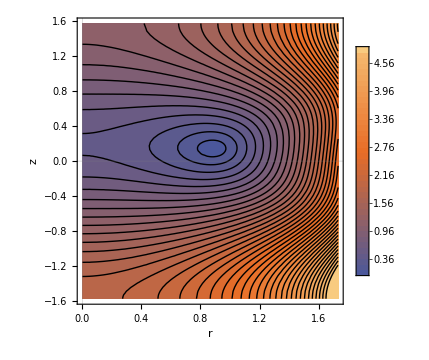

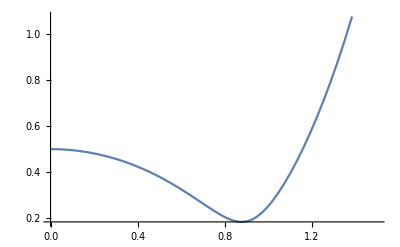
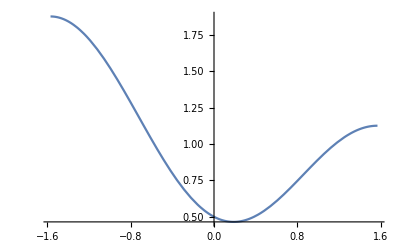

```mathematica
ContourPlot[fieldMagAACyl[r,0,z],{r,0,Sqrt[3]},{z,-π/k,π/k},Contours->40,PlotPoints->10,MaxRecursion->2,PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->"Scientific",FrameLabel->{Style[r,20],Style[z,20]},ImageSize->Medium]
{Plot[fieldMagAACyl[r,0,0],{r,0,1.5}],Plot[fieldMagAACyl[0,0,z],{z,-π/k,π/k}]}
```

```mathematica
(*Locating the points where |B| = 0*)
(*fieldZeroPt=FindRoot[fieldMagCylVA[r,0,0],{r,1.2}];
Print[fieldZeroPt[[1]][[2]],"; |B|=",fieldMagCylVA[r,0,0]/.fieldZeroPt ]*)
(*Locating the saddle points*)
(*fieldZeroPt=FindRoot[{D[fieldMagCylVA[r,0,z],r]==0,D[fieldMagCylVA[r,0,z],z]==0},{{r,1.2},{z,0}}];
Print[fieldZeroPt,"; |B|=",fieldMagCylVA[r,0,0]/.fieldZeroPt ]*)
cplot3d=ContourPlot3D[fieldMagAACyl[r,θ,z],{r,0,1.5},{θ,-2.*π,2.*π},{z,-1.5*(L/2),1.5*(L/2)},Contours->{h0+0.1*(h1-h0)},PlotPoints->5,MaxRecursion->1,ContourStyle->{Opacity[0.8]},PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->{"Scientific"},AxesLabel->{Style[r,25],Style[θ,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},ImageSize->300]
(*cplot3d=ContourPlot3D[fieldMagCarAA[x,y,z],{x,-2,2},{y,-2,2},{z,-1.5*(L/2),1.5*(L/2)},Contours->{h0+0.001},PlotPoints->5,MaxRecursion->2,ContourStyle->{Opacity[0.7]},PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->{"Scientific"},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},TicksStyle->Directive[Gray,15], FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},ImageSize->400];
cplot3dModBSigma=Show[sigmaPM,cplot3d,PlotRange->{{-1.25,1.25},{-1.25,1.25},{-1.25 L/2,1.25 L/2}},PlotTheme->{"Scientific"},AxesLabel->{Style[x,32],Style[y,32],Style[z,32]},FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},Mesh-> None,MeshStyle->Gray,AspectRatio->1,AxesStyle->Directive[Gray,FontSize->25],ImageSize->Large]*)
(*Export["~/Documents/magnetic-mirror/mmmodel1958-nonaxisym-sigma.png",cplot3dModBSigma,"PNG"]*)
(*modBSigmaPM3d=Show[sigmaPM,cplot3d,PlotRange->{{-fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-1.25 L/2,1.25 L/2}},PlotTheme->{"Scientific"},AxesLabel->{Style[x,32],Style[y,32],Style[z,32]},FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},Mesh-> None,MeshStyle->Gray,AxesStyle->Directive[Gray,FontSize->25],ImageSize->Large]*)
```

-Graphics3D-

### Hyperbolic periodic orbit and it' s manifolds of the first-order GCM

#### Solving for the saddle equilibria and its eigenvalues/vectors

```mathematica
mutilde = 10.^-2;
modB[x_,y_,z_] = fieldMagAACar[x,y,z];
b[x_,y_,z_] =fieldAxiAsymCar[x,y,z]/modB[x,y,z];
gradModB[x_,y_,z_]= Simplify[Grad[modB[x,y,z],{x,y,z}]];
bCrossGradModB[x_,y_,z_] = Cross[b[x,y,z],gradModB[x,y,z]] ;
curlb[x_,y_,z_] = Curl[b[x,y,z],{x,y,z}];
tildeB[x_,y_,z_,vpar_]=fieldAxiAsymCar[x,y,z] +Sqrt[mutilde]*vpar*curlb[x,y,z];
tildeBpar[x_,y_,z_,vpar_] = Dot[tildeB[x,y,z,vpar], b[x,y,z]];
Eqn1=x'[t]==(vpar[t]*tildeB[x[t],y[t],z[t],vpar[t]][[1]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[1]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
Eqn2=y'[t]==(vpar[t]*tildeB[x[t],y[t],z[t],vpar[t]][[2]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[2]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
Eqn3=z'[t]==(vpar[t]*tildeB[x[t],y[t],z[t],vpar[t]][[3]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[3]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
Eqn4=vpar'[t]==-(Dot[tildeB[x[t],y[t],z[t],vpar[t]],gradModB[x[t],y[t],z[t]]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
eqpt=FindRoot[{Eqn1,Eqn2,Eqn3,Eqn4}/.{x'[t]->0,y'[t]->0,z'[t]->0,vpar'[t]->0},{{x[t],10.^-12},{y[t],0},{z[t],L/2},{vpar[t],0}}]
jacobianEOM=D[{Eqn1[[2]],Eqn2[[2]],Eqn3[[2]],Eqn4[[2]]},{{x[t],y[t],z[t],vpar[t]}}];
Chop[MatrixForm[jacobianEOM/.eqpt]]
{vals,vecs}=Eigensystem[N[Chop[jacobianEOM/.eqpt]]]
Det[N[jacobianEOM/.eqpt]]
energyTopSaddle=fieldMagAACar[x[t],y[t],z[t]]/.eqpt[[1;;3]]
(*targetEnergy= energyTopSaddle +2*10.^-5;*)
targetEnergy= energyTopSaddle + 0.001
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^(3/2) encountered.

FindRoot::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {x[t],y[t],z[t],vpar[t]} = {0.,0.,1.5708,0.}.

{x[t]→1.×10^-12,y[t]→0.,z[t]→1.5708,vpar[t]→0.}

(0 | -0.0722222 | 0 | 0
0.0722222 | 0 | 0 | 0
0 | 0 | 0 | 1.
0 | 0 | 1.625 | 0)

{{-1.27475,1.27475,0.+0.0722222 ⅈ,0.-0.0722222 ⅈ},{{0.+0. ⅈ,0.+0. ⅈ,-0.617213+0. ⅈ,0.786796+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.617213+0. ⅈ,0.786796+0. ⅈ},{0.707107+0. ⅈ,0.-0.707107 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.707107+0. ⅈ,0.+0.707107 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}}

-0.00847608

1.125

```mathematica
(*targetEnergy= 1.1188730639032358 + 2*10.^-5;*)
targetEnergy= energyTopSaddle + 0.001;
cplot3dCar=ContourPlot3D[fieldMagAACar[x,y,z],{x,-.2,.2},{y,-.3,.3},{z,-1.5*(π/k),1.5*(π/k)},Contours->{targetEnergy},PlotPoints->5,MaxRecursion->2,ContourStyle->{Opacity[0.8]},PlotLegends->Automatic,Mesh-> None,MeshStyle->Gray,PlotTheme->{"Scientific"},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},ImageSize->300]
```

-Graphics3D-

```mathematica
(*targetEnergy = energyTopSaddle+2*10.^-5*)
targetEnergy= energyTopSaddle + 0.001;
(*targetEnergy = h0+10.^-5*(h1-h0);*)
cplot3dCar=ContourPlot3D[fieldMagAACar[x,y,z],{x,-0.1,0.1},{y,0.1,0.15},{z,-1.0*(π/k),1.5*(π/k)},Contours->{targetEnergy},PlotPoints->5,MaxRecursion->2,ContourStyle->{Opacity[0.7]},PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->{"Scientific"},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},AspectRatio->Equal,ImageSize->300]
```

-Graphics3D-

```mathematica
Show[sigmaPlot3d ,cplot3dCar,PlotRange->{{-0.5,0.5},{-0.5,0.5},{-1.5*(π/k),1.5*(π/k)}},PlotTheme->{"Scientific"},AxesLabel->{Style[x,32],Style[y,32],Style[z,32]},FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},Mesh-> None,MeshStyle->Gray,AxesStyle->Directive[Gray,FontSize->25],ImageSize->Large]
```

-Graphics3D-

#### Equation of motion for the PO on \Sigma^-

```mathematica
Clear[po,tEvent];
tEvent = 0;
h0=fieldMagAACyl[r,θ,z]/.saddleTop[[2]];
h1=fieldMagAACyl[r,θ,z]/.saddleBot[[2]];
(*DOPRIamat={
{1/5},
{3/40,9/40},
{44/45,-56/15,32/9},
{19372/6561,-25360/2187,64448/6561,-212/729},
{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DOPRIcvec = {1/5,3/10,4/5,8/9,1, 1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5, p_]:=
N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec}, p];*)
zGuess = L/2.;xGuess = 0.;
yGuess =FindRoot[targetEnergy-fieldMagAACar[xGuess,y,zGuess],{y,0.1},AccuracyGoal->20][[1]][[2]]
tFinal =1.*((2*π)/Im[vals[[3]]])
guessCoord={xGuess,yGuess,zGuess,0.}
(*guessCoord = eqpt[[All,2]] + 10.^-6*Re[vecs[[3]]]*)
(*Eqn1SigmaMinus=x'[t]==(vpar[t]*fieldAxiAsymCar[x[t],y[t],z[t]][[1]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[1]])/fieldMagCarAA[x[t],y[t],z[t]];
Eqn2SigmaMinus=y'[t]==(vpar[t]*fieldAxiAsymCar[x[t],y[t],z[t]][[2]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[2]])/fieldMagCarAA[x[t],y[t],z[t]];
Eqn3SigmaMinus=z'[t]==(vpar[t]*fieldAxiAsymCar[x[t],y[t],z[t]][[3]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[3]])/fieldMagCarAA[x[t],y[t],z[t]];
Eqn4SigmaMinus=vpar'[t]==-(Dot[fieldAxiAsymCar[x[t],y[t],z[t]],gradModB[x[t],y[t],z[t]]])/fieldMagCarAA[x[t],y[t],z[t]];*)Eqn1SigmaMinus=x'[t]==(Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[1]])/fieldMagAACar[x[t],y[t],z[t]];
Eqn2SigmaMinus=y'[t]==(Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[2]])/fieldMagAACar[x[t],y[t],z[t]];
Eqn3SigmaMinus=z'[t]==(Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[3]])/fieldMagAACar[x[t],y[t],z[t]];
Eqn4SigmaMinus=vpar'[t]==0;
po=First@NDSolve[{Eqn1SigmaMinus,Eqn2SigmaMinus,Eqn3SigmaMinus,Eqn4SigmaMinus,x[0]==guessCoord[[1]],y[0]==guessCoord[[2]],z[0]==guessCoord[[3]],vpar[0]==guessCoord[[4]],WhenEvent[Sqrt[(x[t]-xGuess)^2+(y[t]-yGuess)^2]<10.^-20,{Print[t],tEvent=t,"StopIntegration"},"DetectionMethod"->"DerivativeSign","LocationMethod"->"Brent"]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},AccuracyGoal->18,PrecisionGoal->30,Method->{"ExplicitRungeKutta","DifferenceOrder"->8},InterpolationOrder->All]
(*po=First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==guessCoord[[1]],y[0]==guessCoord[[2]],z[0]==guessCoord[[3]],vpar[0]==guessCoord[[4]],WhenEvent[Abs[z[t]-π/k]>10.^-3,{"StopIntegration",Print[t],tEvent=t},"DetectionMethod"->"DerivativeSign","LocationMethod"->"Brent"]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},MaxStepSize->0.01,AccuracyGoal->16,Method->{"StiffnessSwitching", Method->{"ExplicitRungeKutta", Automatic}}]*)
(*po=First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==guessCoord[[1]],y[0]==guessCoord[[2]],z[0]==guessCoord[[3]],vpar[0]==guessCoord[[4]]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},MaxStepSize->0.01,AccuracyGoal->16,Method->{"StiffnessSwitching", Method->{"ExplicitRungeKutta", Automatic}}]*)
```

0.049596

86.998

{0.,0.049596,1.5708,0.}

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t],vpar[t]→InterpolatingFunction[…][t]}

```mathematica
(*x0={x[t],y[t],z[t],vpar[t]}/.po/.t->tEvent
po1=First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==x0[[1]],y[0]==x0[[2]],z[0]==x0[[3]],vpar[0]==x0[[4]],WhenEvent[Abs[z[t]-π/k]>10.^-3,{"StopIntegration",Print[t],tEvent=t},"DetectionMethod"->"DerivativeSign","LocationMethod"->"Brent"]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},MaxStepSize->0.01,AccuracyGoal->16,Method->{"StiffnessSwitching", Method->{"ExplicitRungeKutta", Automatic}}]*)
```

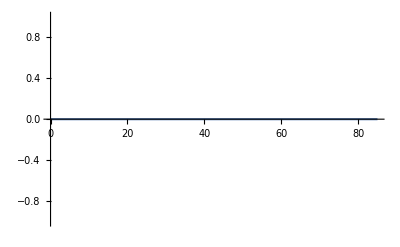

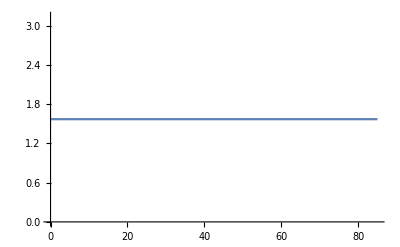

```mathematica
If[tEvent !=0,tFinal = tEvent];
Plot[{vpar[t]}/.po,{t,0,tFinal}]
Plot[{z[t]}/.po,{t,0,tFinal}]
```

-Graphics3D-

-Graphics3D-

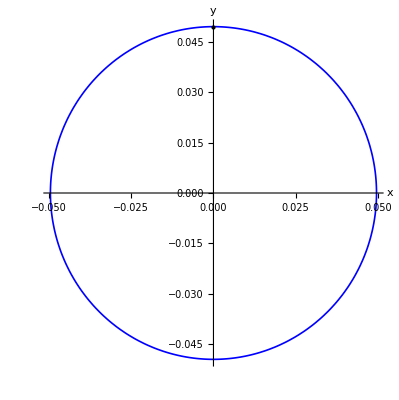

```mathematica
If[tEvent !=0,tFinal = tEvent];
poPlot3d=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.po],{t,0,tFinal},AxesLabel->{x,y,z},PlotRange->{{-0.03,0.03},{0.1,0.15},{π/2-0.1,π/2+0.05}},LabelStyle->{20,GrayLevel[0]},PlotStyle->Directive[Blue,Thickness[0.005]]]
poData = Table[{{x[t],y[t],z[t]}/.po}[[1]],{t,0,tFinal,1}];
Show[cplot3dCar,poPlot3d,PlotRange->{{-.2,.2},{-.1,.3},{π/2-0.1,π/2+0.05}}]
poPlot2d = ParametricPlot[Evaluate[{x[t],y[t]}/.po],{t,0,tFinal},AxesLabel->{x,y},LabelStyle->{10,GrayLevel[0]},PlotStyle->Directive[Blue,Thickness[0.003]]];
Show[poPlot2d,Graphics[Point[{xGuess,yGuess}]]]
Export["hyperbolicPO.txt",poData, "Table","FieldSeparators"->" "];
(*Show[cplot3dCar,poPlot3d,PlotRange->{{-1,1},{-1,1.5},{-1,1.2}}]
Plot[(0.5*vpar[t]^2+fieldMagAACar[x[t],y[t],z[t]])/.po,{t,0,tFinal},PlotRange->{{0,tFinal},{targetEnergy-10.^-10,targetEnergy+10.^-10}},AxesLabel->{t,"Energy"}]*)
```

### Globalising the backward contracting (unstable) manifold

```mathematica
tpGuess = tFinal;
numTrajMani = 50;
idxTrajMani=1;
ti=0;deltati =tpGuess/numTrajMani;
uManiInitCond=ConstantArray[0,{numTrajMani,4}];
While[idxTrajMani<=numTrajMani && ti<tpGuess,
(*phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->ti};*)
uManiInitCond[[idxTrajMani]]={x[t],y[t],z[t],vpar[t]}/.po/.{t->ti} ;
idxTrajMani++;ti=ti+deltati;]
(*Print[uManiInitCond//MatrixForm];*)
tFinalMani = 10*tpGuess;
ti=0;
uManiPlot3d=CreateDataStructure["DynamicArray"];
uManiIntersectParVel0 = ConstantArray[0,{idxTrajMani-1,4}];
For[idx=1,idx<idxTrajMani,idx++,
(*phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->ti+deltati};*)
Print[idx,": ",uManiInitCond[[idx]]];
(*uManiTraj=
First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==uManiInitCond[[idx]][[1]],y[0]==uManiInitCond[[idx]][[2]],z[0]==uManiInitCond[[idx]][[3]],vpar[0]==uManiInitCond[[idx]][[4]],WhenEvent[vpar[t]==0,{"StopIntegration",time2vparzero=t,uManiIntersectParVel0[[idx]]={x[t],y[t],z[t],vpar[t]},Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},AccuracyGoal->16,Method->{"ExplicitRungeKutta","DifferenceOrder"->8},InterpolationOrder->All];*)
uManiTraj=
First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==uManiInitCond[[idx]][[1]],y[0]==uManiInitCond[[idx]][[2]],z[0]==uManiInitCond[[idx]][[3]],vpar[0]==uManiInitCond[[idx]][[4]],WhenEvent[vpar[t]==0,{"StopIntegration",time2vparzero=t,uManiIntersectParVel0[[idx]]={x[t],y[t],z[t],vpar[t]},Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},AccuracyGoal->16,Method->{"StiffnessSwitching", Method->{"ExplicitRungeKutta", Automatic}},InterpolationOrder->All];
Print[idx,": ",uManiIntersectParVel0[[idx]]];
Export["uManiTraj_"<>ToString[idx]<>".txt",Table[{x[t],y[t],z[t],vpar[t]}/.uManiTraj,{t,0,time2vparzero,0.01}], "Table","FieldSeparators"->" "];
uManiPlot3d["Append",ParametricPlot3D[{x[t],y[t],z[t]}/.uManiTraj,{t,0,time2vparzero},AxesLabel->{x,y,z},PlotRange->{{-1,1},{-1,1},{-1,1}},LabelStyle->{20,GrayLevel[0]},PlotStyle->Directive[Magenta,Thickness[0.002]]]]
]
uManiIntersectParVel0 = Append[uManiIntersectParVel0,uManiIntersectParVel0[[1]]];
Export["uManiIntersectParVel0.txt",uManiIntersectParVel0,"Table","FieldSeparators"->" "];
```

1: {1.69407×10^-21,0.049596,1.5708,0.}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 31.6428 and t = 31.8583.

31.7744

1: {-0.0458268,-0.018958,-0.67567,-1.0339×10^-15}

2: {-0.00621945,0.0492045,1.5708,0.}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 31.9272 and t = 32.1619.

32.0374

2: {-0.0426132,-0.0253695,-0.67567,4.42354×10^-15}

3: {-0.0123407,0.0480361,1.5708,0.}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 31.8722 and t = 32.1084.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

31.9814

3: {-0.0392187,-0.0303545,-0.67567,-1.89085×10^-16}

4: {-0.0182671,0.0461094,1.5708,0.}

32.0317

4: {-0.034975,-0.0351603,-0.67567,2.0782×10^-15}

5: {-0.0239052,0.0434547,1.5708,0.}

31.9767

5: {-0.0304454,-0.0391482,-0.67567,1.70621×10^-15}

6: {-0.0291658,0.0401139,1.5708,0.}

32.0651

6: {-0.0250229,-0.0428177,-0.67567,-3.24523×10^-15}

7: {-0.0339659,0.0361397,1.5708,0.}

32.0394

7: {-0.0195405,-0.0455814,-0.67567,7.07767×10^-16}

8: {-0.0382298,0.0315951,1.5708,0.}

32.0499

8: {-0.013634,-0.0476824,-0.67567,-2.40086×10^-15}

9: {-0.0418901,0.0265515,1.5708,0.}

31.9971

9: {-0.0077341,-0.0489865,-0.67567,-2.04003×10^-15}

10: {-0.044889,0.0210888,1.5708,0.}

32.0069

10: {-0.00149483,-0.0495708,-0.67567,-5.55112×10^-17}

11: {-0.0471793,0.0152932,1.5708,0.}

31.9504

11: {0.00453173,-0.0493858,-0.67567,-1.97065×10^-15}

12: {-0.0487246,0.00925606,1.5708,0.}

32.0568

12: {0.0110609,-0.0483441,-0.67567,-9.99201×10^-16}

13: {-0.0495007,0.00307281,1.5708,0.}

31.8803

13: {0.0164406,-0.0467889,-0.67567,-1.61676×10^-15}

14: {-0.0494953,-0.00315895,1.5708,0.}

31.9455

14: {0.0223872,-0.0442528,-0.67567,-1.93335×10^-15}

15: {-0.0487084,-0.00934084,1.5708,0.}

32.0613

15: {0.0281027,-0.0408624,-0.67567,1.97065×10^-15}

16: {-0.0471526,-0.0153753,1.5708,0.}

32.1189

16: {0.033159,-0.0368779,-0.67567,2.08514×10^-15}

17: {-0.0448523,-0.0211669,1.5708,0.}

32.1294

17: {0.0375464,-0.0324,-0.67567,1.34615×10^-15}

18: {-0.0418438,-0.0266244,1.5708,0.}

31.9455

18: {0.0409447,-0.0279826,-0.67567,1.31145×10^-15}

19: {-0.0381747,-0.0316615,1.5708,0.}

32.1462

19: {0.0444542,-0.0219846,-0.67567,6.93889×10^-16}

20: {-0.033903,-0.0361988,1.5708,0.}

32.014

20: {0.0467029,-0.0166834,-0.67567,1.44329×10^-15}

21: {-0.0290959,-0.0401646,1.5708,0.}

31.9703

21: {0.0483924,-0.0108479,-0.67567,-1.18655×10^-15}

22: {-0.0238295,-0.0434962,1.5708,0.}

32.0781

22: {0.0494058,-0.00430892,-0.67567,-6.245×10^-16}

23: {-0.0181869,-0.0461411,1.5708,0.}

31.9104

23: {0.0495758,0.00131986,-0.67567,-1.33227×10^-15}

24: {-0.0122571,-0.0480575,1.5708,0.}

31.9643

24: {0.0489892,0.00771713,-0.67567,-7.07767×10^-16}

25: {-0.00613381,-0.0492152,1.5708,0.}

32.069

25: {0.047529,0.0141597,-0.67567,-7.21645×10^-16}

26: {0.0000863155,-0.0495959,1.5708,0.}

31.7269

26: {0.0458588,0.0188803,-0.67567,-1.39103×10^-16}

27: {0.00630508,-0.0491936,1.5708,0.}

32.047

27: {0.0425514,0.025473,-0.67567,1.99493×10^-15}

28: {0.0124243,-0.0480146,1.5708,0.}

32.0903

28: {0.038925,0.0307301,-0.67567,-4.12777×10^-15}

29: {0.0183474,-0.0460775,1.5708,0.}

32.0291

29: {0.0349204,0.0352146,-0.67567,-1.86309×10^-15}

30: {0.0239807,-0.043413,1.5708,0.}

31.989

30: {0.0303424,0.039228,-0.67567,1.80064×10^-15}

31: {0.0292355,-0.040063,1.5708,0.}

32.0634

31: {0.0249537,0.042858,-0.67567,2.90046×10^-15}

32: {0.0340287,-0.0360806,1.5708,0.}

31.6729

32: {0.0206623,0.045084,-0.67567,-1.30451×10^-15}

33: {0.0382847,-0.0315285,1.5708,0.}

32.029

33: {0.0136231,0.0476855,-0.67567,1.11022×10^-16}

34: {0.0419362,-0.0264786,1.5708,0.}

32.0237

34: {0.00755448,0.0490146,-0.67567,2.05391×10^-15}

35: {0.0449257,-0.0210107,1.5708,0.}

31.9701

35: {0.00154048,0.0495694,-0.67567,2.77556×10^-17}

36: {0.0472058,-0.015211,1.5708,0.}

32.0027

36: {-0.00480429,0.0493601,-0.67567,-3.85803×10^-15}

37: {0.0487407,-0.00917124,1.5708,0.}

32.0204

37: {-0.011018,0.0483539,-0.67567,-2.13718×10^-15}

38: {0.049506,-0.00298665,1.5708,0.}

32.0474

38: {-0.0170857,0.0465572,-0.67567,8.32667×10^-16}

39: {0.0494897,0.00324509,1.5708,0.}

31.9857

39: {-0.0225925,0.0441484,-0.67567,8.46545×10^-16}

40: {0.0486921,0.0094256,1.5708,0.}

32.0058

40: {-0.0280098,0.0409261,-0.67567,-9.85323×10^-16}

41: {0.0471257,0.0154573,1.5708,0.}

32.0019

41: {-0.0329107,0.0370996,-0.67567,3.33067×10^-15}

42: {0.0448154,0.021245,1.5708,0.}

31.9998

42: {-0.0372983,0.0326854,-0.67567,1.14622×10^-15}

43: {0.0417974,0.0266972,1.5708,0.}

32.0413

43: {-0.0411856,0.0276269,-0.67567,3.13638×10^-15}

44: {0.0381196,0.0317279,1.5708,0.}

32.136

44: {-0.0444761,0.0219402,-0.67567,-2.02616×10^-15}

45: {0.0338399,0.0362578,1.5708,0.}

32.0921

45: {-0.0468248,0.0163381,-0.67567,-3.93435×10^-15}

46: {0.029026,0.0402151,1.5708,0.}

32.0048

46: {-0.0484379,0.0106428,-0.67567,-3.58047×10^-15}

47: {0.0237538,0.0435376,1.5708,0.}

31.9497

47: {-0.0493719,0.00468132,-0.67567,7.91034×10^-16}

48: {0.0181065,0.0461727,1.5708,0.}

32.0005

48: {-0.0495632,-0.00172887,-0.67567,-2.08167×10^-15}

49: {0.0121734,0.0480788,1.5708,0.}

31.9385

49: {-0.0489902,-0.00771123,-0.67567,-1.88738×10^-15}

50: {0.00604815,0.0492258,1.5708,0.}

31.9543

50: {-0.0476206,-0.0138482,-0.67567,1.41553×10^-15}

```mathematica
Show[poPlot3d,cplot3dCar,ListPointPlot3D[uManiIntersectParVel0[[All,1;;3]]],Table[uManiPlot3d["Part",idx],{idx,1,numTrajMani}],AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},PlotRange->{{-0.03,0.03},{0.1,0.15},{π/2-0.1,π/2+0.05}},AspectRatio->Equal,AxesStyle->Directive[Gray,FontSize->15],ImageSize->500]
```

-Graphics3D-

### Globalising the forward contracting (stable) manifold

```mathematica
idxTrajMani=1;
dir = 1; (* -1: directed towards positive z*)
del=10.^-12;
ti=0;deltati =tpGuess/numTrajMani;
sManiInitCond=ConstantArray[0,{numTrajMani,4}];
While[idxTrajMani<=numTrajMani && ti<tpGuess,
sManiInitCond[[idxTrajMani]]={x[t],y[t],z[t],vpar[t]}/.po/.{t->ti};
idxTrajMani++;
ti=ti+deltati;]
(*Print[sManiInitCond//MatrixForm];*)
tFinalMani = 10.*tpGuess;
ti=0;
sManiPlot3d=CreateDataStructure["DynamicArray"];
sManiIntersectParVel0 = ConstantArray[0,{idxTrajMani-1,4}];
For[idx=1,idx<idxTrajMani,idx++,
(*phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->ti+deltati};*)
Print[idx,": ",sManiInitCond[[idx]]];
sManiTraj=(*First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==sManiInitCond[[idx]][[1]],y[0]==sManiInitCond[[idx]][[2]],z[0]==sManiInitCond[[idx]][[3]],vpar[0]==sManiInitCond[[idx]][[4]],WhenEvent[vpar[t]==0,{"StopIntegration",time2vparzero=t,sManiIntersectParVel0[[idx]]={x[t],y[t],z[t],vpar[t]},Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,-tFinalMani,0},MaxStepSize->0.01,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];*)
First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==sManiInitCond[[idx]][[1]],y[0]==sManiInitCond[[idx]][[2]],z[0]==sManiInitCond[[idx]][[3]],vpar[0]==sManiInitCond[[idx]][[4]],WhenEvent[vpar[t]==0,{"StopIntegration",time2vparzero=t,sManiIntersectParVel0[[idx]]={x[t],y[t],z[t],vpar[t]},Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,0,-tFinalMani},AccuracyGoal->16,Method->{"StiffnessSwitching", Method->{"ExplicitRungeKutta", Automatic}},InterpolationOrder->All];
Export["sManiTraj_"<>ToString[idx]<>".txt",Table[{x[t],y[t],z[t],vpar[t]}/.sManiTraj,{t,0,time2vparzero,-0.01}], "Table","FieldSeparators"->" "];
sManiPlot3d["Append",ParametricPlot3D[{x[t],y[t],z[t]}/.sManiTraj,{t,time2vparzero,0},AxesLabel->{x,y,z},PlotRange->{{-1,1},{-1,1},{-1,1}},LabelStyle->{20,GrayLevel[0]},PlotStyle->Directive[Green,Thickness[0.002]]]]
]
sManiIntersectParVel0=Append[sManiIntersectParVel0,sManiIntersectParVel0[[1]]];
Export["sManiIntersectParVel0.txt",sManiIntersectParVel0,"Table","FieldSeparators"->" "];
```

1: {1.69407×10^-21,0.049596,1.5708,0.}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = -31.6622 and t = -31.8895.

-31.7792

2: {-0.00621945,0.0492045,1.5708,0.}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = -31.8223 and t = -32.0321.

-32.0037

3: {-0.0123407,0.0480361,1.5708,0.}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = -32.0864 and t = -32.3039.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

-32.1741

4: {-0.0182671,0.0461094,1.5708,0.}

-32.0159

5: {-0.0239052,0.0434547,1.5708,0.}

-32.0666

6: {-0.0291658,0.0401139,1.5708,0.}

-32.0228

7: {-0.0339659,0.0361397,1.5708,0.}

-31.9481

8: {-0.0382298,0.0315951,1.5708,0.}

-32.038

9: {-0.0418901,0.0265515,1.5708,0.}

-32.1241

10: {-0.044889,0.0210888,1.5708,0.}

-32.1115

11: {-0.0471793,0.0152932,1.5708,0.}

-32.0203

12: {-0.0487246,0.00925606,1.5708,0.}

-31.9146

13: {-0.0495007,0.00307281,1.5708,0.}

-32.094

14: {-0.0494953,-0.00315895,1.5708,0.}

-32.0563

15: {-0.0487084,-0.00934084,1.5708,0.}

-32.0712

16: {-0.0471526,-0.0153753,1.5708,0.}

-32.0472

17: {-0.0448523,-0.0211669,1.5708,0.}

-32.134

18: {-0.0418438,-0.0266244,1.5708,0.}

-31.954

19: {-0.0381747,-0.0316615,1.5708,0.}

-32.0194

20: {-0.033903,-0.0361988,1.5708,0.}

-32.0009

21: {-0.0290959,-0.0401646,1.5708,0.}

-32.0671

22: {-0.0238295,-0.0434962,1.5708,0.}

-32.1215

23: {-0.0181869,-0.0461411,1.5708,0.}

-32.0141

24: {-0.0122571,-0.0480575,1.5708,0.}

-32.0214

25: {-0.00613381,-0.0492152,1.5708,0.}

-31.9817

26: {0.0000863155,-0.0495959,1.5708,0.}

-31.8678

27: {0.00630508,-0.0491936,1.5708,0.}

-31.9759

28: {0.0124243,-0.0480146,1.5708,0.}

-31.9644

29: {0.0183474,-0.0460775,1.5708,0.}

-32.0762

30: {0.0239807,-0.043413,1.5708,0.}

-32.0048

31: {0.0292355,-0.040063,1.5708,0.}

-32.1237

32: {0.0340287,-0.0360806,1.5708,0.}

-31.965

33: {0.0382847,-0.0315285,1.5708,0.}

-32.0142

34: {0.0419362,-0.0264786,1.5708,0.}

-32.02

35: {0.0449257,-0.0210107,1.5708,0.}

-32.1231

36: {0.0472058,-0.015211,1.5708,0.}

-32.0865

37: {0.0487407,-0.00917124,1.5708,0.}

-32.0006

38: {0.049506,-0.00298665,1.5708,0.}

-32.0112

39: {0.0494897,0.00324509,1.5708,0.}

-31.9762

40: {0.0486921,0.0094256,1.5708,0.}

-32.1032

41: {0.0471257,0.0154573,1.5708,0.}

-32.0196

42: {0.0448154,0.021245,1.5708,0.}

-32.0198

43: {0.0417974,0.0266972,1.5708,0.}

-32.0773

44: {0.0381196,0.0317279,1.5708,0.}

-32.0433

45: {0.0338399,0.0362578,1.5708,0.}

-32.026

46: {0.029026,0.0402151,1.5708,0.}

-32.0487

47: {0.0237538,0.0435376,1.5708,0.}

-32.1097

48: {0.0181065,0.0461727,1.5708,0.}

-31.9431

49: {0.0121734,0.0480788,1.5708,0.}

-32.0169

50: {0.00604815,0.0492258,1.5708,0.}

-32.0429

```mathematica
xMinPlt=Min[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]
xMaxPlt =Max[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]
yMinPlt =Min[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]
yMaxPlt =Max[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]
```

-0.0155624

0.0155626

0.115128

0.129331

```mathematica
(*Show[cplot3dCar,ListPointPlot3D[sManiIntersectParVel0[[All,1;;3]],PlotStyle->Directive[Green,PointSize[0.01]]],ListPointPlot3D[uManiIntersectParVel0[[All,1;;3]],PlotStyle->Directive[Magenta,PointSize[0.01]]],Table[uManiPlot3d["Part",idx],{idx,1,numTrajMani}],Table[sManiPlot3d["Part",idx],{idx,1,numTrajMani}],PlotRange->{{xMinPlt-0.03,xMaxPlt+0.03},{yMinPlt-0.05,yMaxPlt+0.1},{-1.,2.}},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],AspectRatio->Equal,ImageSize->500]*)
Show[cplot3dCar,ListPointPlot3D[sManiIntersectParVel0[[All,1;;3]],PlotStyle->Directive[Green,PointSize[0.01]]],ListPointPlot3D[uManiIntersectParVel0[[All,1;;3]],PlotStyle->Directive[Magenta,PointSize[0.01]]],Table[uManiPlot3d["Part",idx],{idx,1,numTrajMani}],Table[sManiPlot3d["Part",idx],{idx,1,numTrajMani}],AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],AspectRatio->Equal,ImageSize->500]
```

-Graphics3D-

-Graphics3D-

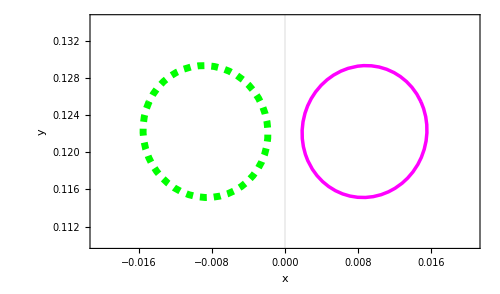

```mathematica
offset = 0.005;
Show[cplot3dCar,ListLinePlot3D[sManiIntersectParVel0[[All,1;;3]],PlotStyle->Directive[Green,Dashed,Thickness[0.015]]],ListLinePlot3D[uManiIntersectParVel0[[All,1;;3]],PlotStyle->Directive[Magenta,Thickness[0.008]]],PlotRange->{{Min[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]-offset,Max[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]+offset},{Min[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]-offset,Max[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]+offset},{-0.70,-0.65}},AxesLabel->{Style[x,35],Style[y,35],Style[z,35]},AxesStyle->Directive[Gray,FontSize->18],AspectRatio->Equal,ImageSize->500]
Show[{ListLinePlot[sManiIntersectParVel0[[All,1;;2]],PlotStyle->Directive[Green,Dashed,Thickness[0.01]],PlotTheme->{"Scientific"}],ListLinePlot[uManiIntersectParVel0[[All,1;;2]],PlotStyle->Directive[Magenta,Thickness[0.005]],PlotTheme->{"Scientific"}]},PlotRange->{{Min[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]-offset,Max[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]+offset},{Min[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]-offset,Max[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]+offset}},FrameLabel->{Style[x,35],Style[y,35]},FrameStyle->Directive[Gray,FontSize->15],AspectRatio->Equal,ImageSize->500]
```